# Motion with a drag. Starter code. Free Fall

## Use Kinematic Equation

```mathematica
SetDirectory[NotebookDirectory[]];
g = - 9.8;
yKin[t_, y0_, v0_]:=y0 +v0 t + (g t^2)/2;
Plot[yKin[t, 0, 0], {t, 0, 2}, AxesLabel->{"t, s", "y, m"}];
```

## Use differential equation

```mathematica
s=NDSolve[{y''[t]==g,y[0]==0, y'[0]==0},y,{t,0,5}];
Plot[Evaluate[y[t]/.s],{t,0,3},PlotRange->All, AxesLabel->{"t, s", "y, m"}];
```

## Show together

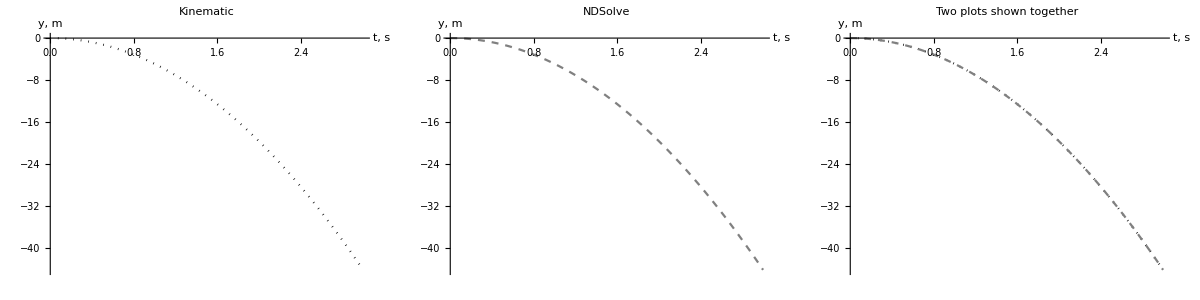

```mathematica
p1 =Plot[yKin[t, 0, 0], {t, 0, 3}, PlotStyle -> {Black, Dotted},  AxesLabel->{"t, s", "y, m"}, ImageSize->300, PlotLabel->"Kinematic"];
p2 =  Plot[Evaluate[y[t]/.s],{t,0,3}, PlotStyle -> {Gray, Dashed},  AxesLabel->{"t, s", "y, m"}, ImageSize->300, PlotLabel->"NDSolve"];
p3=Show[p1, p2, PlotLabel->"Two plots shown together"];
p4= Deploy@Grid[{{p1,p2, p3}},Dividers->Gray,Spacings->{2,2}]
Export["p4.eps",p4];
```

# Motion with a drag. Add drag.

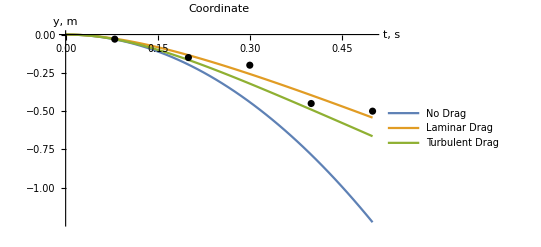
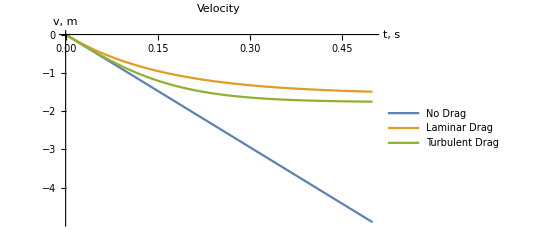
-Graphics- | -Graphics-

```mathematica
(*Students have to read about laminar or turbulent flow, Reynolds number*)
k=1;(*Students should think how to choose this constant?*)
ρ=1 (*Students should choose an appropriate value for air or water*);
Subscript[C, D]=1;(*Students have to learn how to choose this drag constant*)
A=π (0.01)2;(*cross section area*)
m=0.01;

LaminarDrag[v_]:=-k v A
TurbulentDrag[v_]:=-Sign[v] 1/2 ρ v^2 Subscript[C, D] A

Subscript[F, g]=m g;
Tmax = 0.5;

(* Solve *)
sFree=NDSolve[{y''[t]==Subscript[F, g]/m,y[0]==0, y'[0]==0},y,{t,0,Tmax}];
sL=NDSolve[{y''[t]==(Subscript[F, g]+ LaminarDrag[y'[t]])/m,y[0]==0, y'[0]==0},y,{t,0,Tmax}];
sT=NDSolve[{y''[t]==(Subscript[F, g]+ TurbulentDrag[y'[t]])/m,y[0]==0, y'[0]==0},y,{t,0,Tmax}];

(*acutual data*)
data = Import["sample.csv"];  (* use //Table to see it as a table *)
pdata = ListPlot[data, PlotStyle->Black];

(* Plot *)
pY = Show[ Plot[{Evaluate[y[t]/.sFree], Evaluate[y[t]/.sL], Evaluate[y[t]/.sT]},{t,0,Tmax},
PlotRange->All, PlotLegends->{"No Drag", "Laminar Drag", "Turbulent Drag"}, AxesLabel->{"t, s", "y, m"}, ImageSize->400, PlotLabel->"Coordinate"],
pdata];

pV = Plot[{Evaluate[y'[t]/.sFree], Evaluate[y'[t]/.sL], Evaluate[y'[t]/.sT]},{t,0,Tmax},
PlotRange->All, PlotLegends->{"No Drag", "Laminar Drag", "Turbulent Drag"}, AxesLabel->{"t, s", "v, m"},ImageSize->400,  PlotLabel->"Velocity"];

pp = Deploy@Grid[{{pY,pV}},Dividers->Gray,Spacings->{2,2}]
Export["pp.eps",pp];
```

## Error analysis

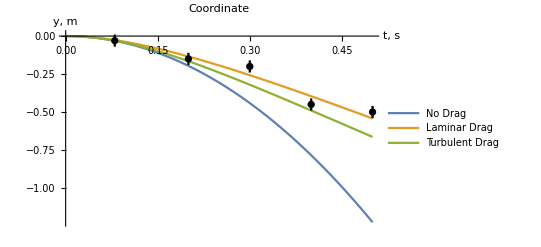
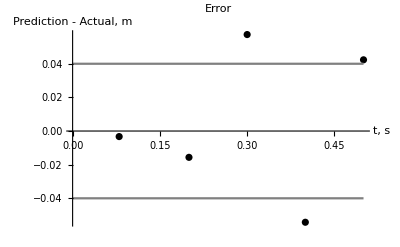
-Graphics- | -Graphics-

```mathematica
dataTime = data[[All, 1]];(* time values in data *)
dataCoordinate = data[[All, 2]]; (* coordinate values in data *)
Prediction = Evaluate[y[ dataTime ]/.sL] [[1]];(* corresponding prediction from simulation *)

StDev = StandardDeviation[Prediction - dataCoordinate]; (* Standart Deviation of a difference *)
MaxPercentageError = Max[100*(Prediction - dataCoordinate)/(0.5*(Prediction + dataCoordinate))];(* Maximum Percentage Error *)

(* add error bar to plot *)
Needs["ErrorBarPlots`"]
InstError = 0.04; (* instrumental error *)
error = ConstantArray[InstError, Length[data]]; (* add instrumental error *) 
(* students can extend this approach to include accidental error, while repeating experiment *)
withError=Transpose[{data[[All,1]],data[[All,2]],error}];
pdataNew = Show[ListPlot[data],ErrorListPlot[withError,PlotStyle->Black]];

(* Plot *)
pYError = Show[ Plot[{Evaluate[y[t]/.sFree], Evaluate[y[t]/.sL], Evaluate[y[t]/.sT]},{t,0,Tmax},
PlotRange->All, PlotLegends->{"No Drag", "Laminar Drag", "Turbulent Drag"}, AxesLabel->{"t, s", "y, m"}, ImageSize->400, PlotLabel->"Coordinate"],
pdataNew];

erp1 = Plot[{InstError}, {x, 0, Tmax}, PlotStyle->Gray]; 
erp2 = Plot[{-InstError}, {x, 0, Tmax}, PlotStyle->Gray];
pError = ListPlot[Transpose[{dataTime,  dataCoordinate-Prediction}], PlotLabel->"Error",AxesLabel->{"t, s", "Prediction - Actual, m"} ,ImageSize->400, PlotStyle->Black];
pErrorT = Show[pError, erp1, erp2];
ppError = Deploy@Grid[{{pYError,pErrorT}},Dividers->Gray,Spacings->{2,2}]
Export["ppError.eps",ppError];
```